```mathematica
deq=x'[t]==x[t]-t;
```

```mathematica
analyticsolution=DSolve[{deq,x[0]==x0},x,t]//FullSimplify;
xanalyticgeneral=x[t]/.analyticsolution[[1]];
```

1-ⅇ^t+t+ⅇ^t x0

```mathematica
print[Αναλυτική Λύση:'', xanalyticgernal];
```

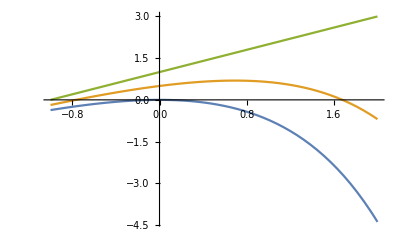

```mathematica
xa1=xanalyticgeneral/.x0->0;
xa2= xanalyticgeneral/.x0->0.5;
xa3=xanalyticgeneral/.x0->1;
tmin=-1 ;  tmax=2 ;
Plot[{xa1,xa2,xa3}, {t,tmin,tmax}]
```

```mathematica
xanalytic[t_]=xanalyticgeneral/.{x0->1/2}
Print["Μερική Λύση: x=",xpartial]
gr1=Plot[xanalytic[t]]
```

1-ⅇ^t/2+t

Μερική Λύση: x=xpartial

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[xanalytic[t]]

```mathematica
xEuler=Interpolation[dat]
gr3=Plot[xEuler[t],{t,t0,tmax},Plotstyle->{RGBColor[1,0,O]}]
```

Interpolation::innd: First argument in dat does not contain a list of data and coordinates.

Interpolation[dat]

Plot::optx: Unknown option Plotstyle→{RGBColor[1,0,O]} in Plot[xEuler[t],{t,t0,tmax},Plotstyle→{RGBColor[1,0,O]}].

Plot[xEuler[t],{t,t0,tmax},Plotstyle→{RGBColor[1,0,O]}]

```mathematica
Clear[x,t]
deq=x'[t]==x[t]-t
t0=0;xo=1/2;tmax=3;
sol2=NDSolve[[deq]]
```

Sin[x[t]]+x''[t]==0

3.09212

{{x→InterpolatingFunction[…]}}

InterpolatingFunction[…][t]

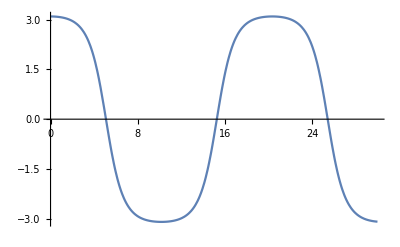

```mathematica
deq=x''[t]+Sin[x[t]]==0
x0=π/1.016

p0=0;
tmax=30;
sol=NDSolve[{deq,x[0]==x0,x'[0]==p0},x,{t,0,tmax}]
xt[t_]=x[t]/.sol[[1]]
Plot[xt[t],{t,0,tmax}]
```

Sin[x[t]]+x''[t]==0

NDSolve::mxst: Maximum number of 1000 steps reached at the point t == 116.93.

{{x→InterpolatingFunction[…]}}

InterpolatingFunction[…][t]

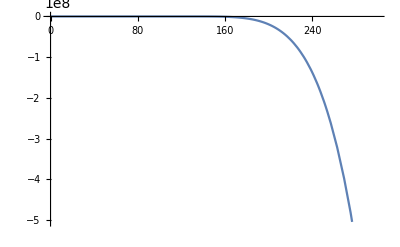

```mathematica
deq=x''[t]+Sin[x[t]]==0
x0=π/6;
p0=0;
tmax=300;
sol=NDSolve[{deq,x[0]==x0,x'[0]==p0},x,{t,0,tmax},MaxSteps->1000]
xt[t_]=x[t]/.sol[[1]]
Plot[xt[t],{t,0,tmax}]
```

Sin[x[t]]+x''[t]==0

-1/100000+π

{{x→InterpolatingFunction[{{0., 3000.}}, <>]}}

InterpolatingFunction[{{0., 3000.}}, <>][t]

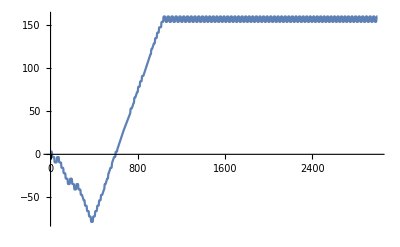

```mathematica
deq=x''[t]+Sin[x[t]]==0
x0=π-10^-5

p0=0;
tmax=3000;
sol=NDSolve[{deq,x[0]==x0,x'[0]==p0},x,{t,0,tmax},MaxSteps->Infinity]
xt[t_]=x[t]/.sol[[1]]
Plot[xt[t],{t,0,tmax}]
```

Sin[x[t]]+x''[t]==0

-1/100000+π

{{x→InterpolatingFunction[…]}}

InterpolatingFunction[…][t]

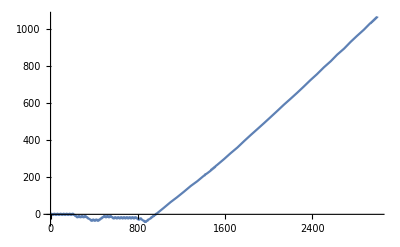

```mathematica
deq=x''[t]+Sin[x[t]]==0
x0=π-10^-5

p0=0;
tmax=3000;
sol=NDSolve[{deq,x[0]==x0,x'[0]==p0},x,{t,0,tmax},MaxSteps->Infinity,AccuracyGoal->6,PrecisionGoal->6]
xt[t_]=x[t]/.sol[[1]]
Plot[xt[t],{t,0,tmax}]
```

Sin[x[t]]+x''[t]==0

-1/100000+π

{{x→InterpolatingFunction[…]}}

InterpolatingFunction[…][t]

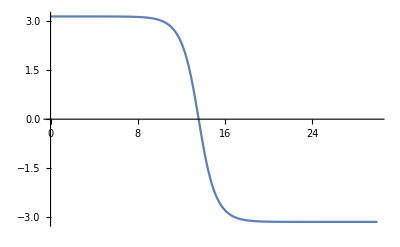

```mathematica
deq=x''[t]+Sin[x[t]]==0
x0=π-10^-5

p0=0;
tmax=30;
sol=NDSolve[{deq,x[0]==x0,x'[0]==p0},x,{t,0,tmax},MaxSteps->Infinity,AccuracyGoal->12,PrecisionGoal->12]
xt[t_]=x[t]/.sol[[1]]
Plot[xt[t],{t,0,tmax}]
```